```mathematica
ClearAll["Global'*"]
deq1=x'[t]==x[t]*(y[t]-1)-0.2
deq2=y'[t]==(1+1.2*y[t]-2*x[t])*y[t]
```

x'[t]==-0.2+x[t] (-1+y[t])

y'[t]==y[t] (1-2 x[t]+1.2 y[t])

```mathematica
XS1=-0.2;
YS1=0;
```

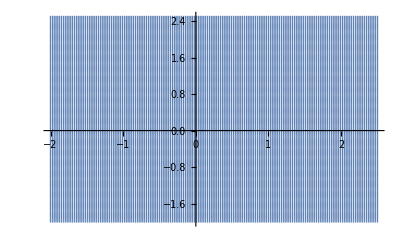

```mathematica
XS2=-0.1;
YS2=-1;

XS3=1.2;
YS3=1.166667;

arxikes=Table[{x0,y0},{x0,-2,2.5,0.03},{y0,-2,2.5,0.02}];
arxikes=Flatten[arxikes,1];
ListPlot[arxikes]
```

```mathematica
n=Length[arxikes]
```

2907

```mathematica
per1={{XS1,YS1}};
```

```mathematica
per2={{XS2,YS2}};
```

```mathematica
per3={{XS3,YS3}};
```

```mathematica
per4={};
```

NDSolve::ndsz: At t == 0.902534, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {4} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At t == 0.678503, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {4} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.571886, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

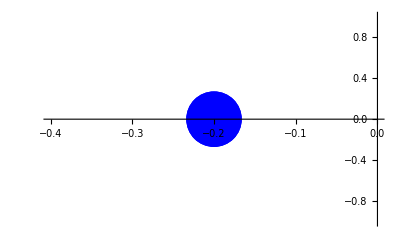

```mathematica
tmax=4;
For[i=1,i<=n,i++,
x0=arxikes[[i,1]]; y0=arxikes[[i,2]];
sol=NDSolve[{deq1,deq2,x[0]==x0,y[0]==y0},{x,y},{t,0,tmax,20},Method->"StiffnessSwitching"];
xt=x/.sol[[1]]; yt=y/.sol[[1]];
Xf=xt[tmax]; Yf=yt[tmax];
d1=Sqrt[(Xf-XS1)^2+(Yf-YS1)^2];
d2=Sqrt[(Xf-XS2)^2+(Yf-YS2)^2];
d3=Sqrt[(Xf-XS3)^2+(Yf-YS3)^2];
Which[d1<0.005,AppendTo[per1,{x0,y0}],d2<0.005, AppendTo[per2,{x0,y0}],d3<0.005,AppendTo[per3,{x0,y0}],d1>0.005&&d2>0.005&&d3>0.005,AppendTo[per4,{x0,y0}]]]
Short[per1];
Short[per2];
Short[per3];


set1=ListPlot[per1,PlotStyle->{Blue,PointSize[0.1]}]
```

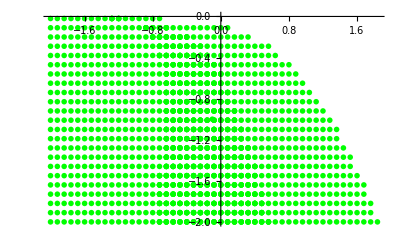

```mathematica
set2=ListPlot[per2,PlotStyle->{Green,PointSize[0.01]}]
```

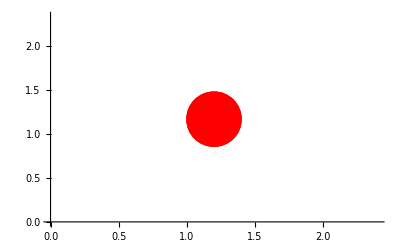

```mathematica
set3=ListPlot[per3,PlotStyle->{Red,PointSize[0.1]},PlotRange->Full]
```

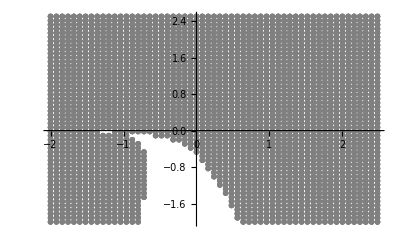

```mathematica
set4=ListPlot[per4,PlotStyle->{Gray,PointSize[0.01]}]
```

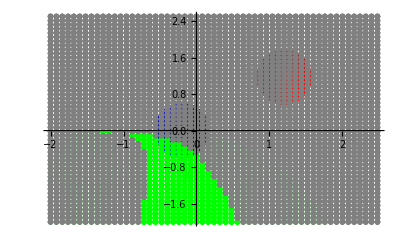

```mathematica
Show[{set1,set2,set3,set4},PlotRange->Full]
```